# String Conditional BDM.

## String BDM.

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Dropbox\PostDoc\MathematicaNB\conditionalBDM

```mathematica
D5 = <<"D5.m";
```

Adding missing strings:

```mathematica
D5=Flatten/@Append[D5,{{"000110100111",(5.21946101832149*^-12)}}];
D5=Flatten/@Append[D5,{{"111001011000",(5.21946101832149*^-12)}}];
```

```mathematica
Table[HashStrings[D5[[i,1]]] = -Log[2,D5[[i,2]]],{i,Length@D5}];
```

```mathematica
(* Table[HashStrings[D4[[i,1]]] = -Log[2,D4[[i,2]]],{i,Length@D4}]; *)
```

```mathematica
(* Table[HashStrings[D3[[i,1]]] = -Log[2,D3[[i,2]]],{i,Length@D3}]; *)
```

Strings of length 12 not appearing:

```mathematica
N@HashStrings["000"]
```

5.39619

```mathematica
StringBDM[string_,len_:1]:= 
N@Total[HashStrings[#[[1]]]+Log[2,#[[2]]]&/@Tally[If[TrueQ[StringLength[string]>12],StringPartition[string,12,len],{string}]]]
```

## Conditional String BDM.

Functions to parse through shared members.

```mathematica
NotIn[List[],rep_]:= List[]
```

```mathematica
NotIn[x_,rep_]:=If[MemberQ[rep,x[[1]]],NotIn[x[[2;;]],rep],Prepend[NotIn[x[[2;;]],rep],x[[1]]]]
```

```mathematica
Shrd[List[],rep_]:=List[]
```

```mathematica
Shrd[x_,rep_]:= If[MemberQ[rep,x[[1]]],Prepend[Shrd[x[[2;;]],rep],x[[1]]],Shrd[x[[2;;]],rep]]
```

```mathematica
RepM[x_,y_]:= If[x==y,1,x] (* Hack given that Log[1]=0 *)
```

### Conditional String BDM function.

```mathematica
Remove[StringBDMC]
```

```mathematica
StringBDMC[string_,string2_,len_:1]:= 
N@Block[{ln= Min[12, StringLength[string2]]},
Block[{
part = StringPartition[string,ln,len],
part2 = StringPartition[string2,ln,len],
ay = Tally[StringPartition[string2,ln,len]]
},
Block[{t =Table[ny[ay[[i]][[1]]]=ay[[i]][[2]],{i,Length[ay]}]},
If[Length[Shrd[part, part2]]==0,StringBDM[string,len],
Total[(HashStrings[#[[1]]]+Log[2,#[[2]]])&/@Tally[NotIn[part, part2]]]
+ Total[Log[2,RepM[#[[2]],ny[#[[1]]]]]&/@Tally[Shrd[part, part2]]]
]
]
]
]
```

```mathematica
StringBDMC["010101010101010101111","010",3]
```

14.0715

The next definition allows for setting a partition size.

```mathematica
StringBDMC2[string_,string2_,partSize_,len_:1]:= 
N@Block[{
part = StringPartition[string,partSize,len],
part2 = StringPartition[string2,partSize,len],
ay = Tally[StringPartition[string2,partSize,len]]
}, 
Block[{t =Table[ny[ay[[i]][[1]]]=ay[[i]][[2]],{i,Length[ay]}]},
Total[(HashStrings[#[[1]]]+Log[2,#[[2]]])&/@Tally[NotIn[part, part2]]]
+ Total[Log[2,RepM[#[[2]],ny[#[[1]]]]]&/@Tally[Shrd[part, part2]]]
]
]
```

```mathematica
StringBDMC2["010101010101010101111","000",3,3]
```

19.5769

## Experiments.

Lets start with a random string.

```mathematica
SeedRandom[07082018]
```

```mathematica
random[n_] := RandomInteger[{0,1},n]
```

```mathematica
r1 = random[20]
```

{1,1,0,0,0,1,0,1,1,1,0,1,1,1,0,1,0,1,0,1}

As expected, the conditional entropy and conditional BDM of this random string with itself should be 0.

```mathematica
Statistics`Library`NConditionalEntropy[r1,r1]
```

0.

```mathematica
r1S = StringJoin[Map[ToString,r1]]
```

11000101110111010101

```mathematica
StringBDMC[r1S,r1S,3]
```

0.

The partition size doesn’t matter.

```mathematica
Table[StringBDMC2[r1S,r1S,i,1],{i,20}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

We can use a randomly generated string as a base to bigger strings. Conditional entropy should be now higher than zero with respect to the smaller, base string.

```mathematica
rSmall = random[5]
```

{0,0,1,1,1}

```mathematica
rLarge =Flatten[RandomChoice[{rSmall},4]]
```

{0,0,1,1,1,0,0,1,1,1,0,0,1,1,1,0,0,1,1,1}

```mathematica
rSmallS = StringJoin[Map[ToString,rSmall]]
```

00111

```mathematica
rLargeS = StringJoin[Map[ToString,rLarge]]
```

00111001110011100111

```mathematica
Statistics`Library`NConditionalEntropy[rLarge,rSmall]
```

2.67549

```mathematica
StringBDMC[rLargeS,rSmallS,StringLength[rSmallS]]
```

2.

### Why Conditional BDM Works Over Different Partition Sizes, while Conditional Entropy Does Not.

Now, I will analyze the behavior of conditional BDM and conditional Entropy over different partition sizes.

```mathematica
ConditionalEntropyOfSize[s1_, s2_, pSize_, d_]:=Block[
{
p1 =Partition[s1,pSize,d],
p2 = Partition[s2,pSize,d]
},
Statistics`Library`NConditionalEntropy[p1,p2]
]
```

We will generate a second random binary string. With high probability, we do not expect them to have shared information.

```mathematica
r2 = random[20]
```

{1,0,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,0,1,0}

```mathematica
r2S= StringJoin[Map[ToString,r2]]
```

10101101011010111010

```mathematica
Statistics`Library`NConditionalEntropy[r1,r2]
```

0.924511

However, we encounter a problem with the built in Mathematica conditional Entropy function.

```mathematica
ConditionalEntropyOfSize[r1, r2, 5, 5]
```

0.

The value from above should not be zero. This is caused by the way  Mathematica computes entropy, lets look closer at each of the two strings:

```mathematica
x=Map[StringJoin[ToString/@#]&,Partition[r1,5,5]]
```

{11000,10111,01110,10101}

```mathematica
y =Map[StringJoin[ToString/@#]&,Partition[r2,5,5]]
```

{10101,10101,10101,11010}

As we can see, each member are a different symbol therefore the inferred distributions are the same and each give no additional information over the other.

I spent perhaps too much time trying to solve this problem, but I reached the conclusion that joint entropy is not defined for distributions with different alphabets, which is the case we have above. This is an important advantage of conditional BDM, as we are using the universal distribution with applies to all computable objects.

For this reason, I will use the Normalized Compression Distance as a comparison point instead.

### Compared with Normalized Compression Distance.

We can define the Normalized Compression Distance as follows:

```mathematica
NCD[x_,y_]:=Block[{
cx = StringLength[Compress[x]],
cy=StringLength[Compress[y]],
cxy = StringLength[Compress[Join[x,y]]]
},
(cxy-Min[cx,cy])/Max[cx,cy]
]
```

```mathematica
NCD[r1S,r1S]
```

8/21

```mathematica
NCD[r1S,r2S]
```

16/21

```mathematica
NCD[rLargeS,rSmallS]
```

10/17

As shown in previous articles, NCD does not work very well on small strings but seems to be keeping the relationship we expect.

```mathematica
StringBDMC[r1S,r2S,12]
```

32.7243

```mathematica
StringBDM[r1S,12]
```

32.7243

#### Conditional BDM over Two Randomly Generated Strings at Different Partitions Settings.

Conditional BDM uses the entropy like behavior of BDM to compute its value. Given the difficulty of computing an approximation of K(x|y), which would require a CTM-like method using Turing Machines with inputs, Conditional BDM can be seen as a generalization of conditional Entropy over the space all computable objects, using the universal distribution as the base distribution.

```mathematica
x = Table[
Mean[
Table[
Block[
{
r1 =  StringJoin[Map[ToString,random[20]]],
r2= StringJoin[Map[ToString,random[20]]],
nPar = Length[Partition[r1,i,i]]
},
StringBDMC2[r1, r2, i, i]/nPar (* we divide between the approximate number of paritions.*)
]
,{j,5000}(* Number of samples *)
] //N
],{i,20}
]
```

{0.286615,0.446625,2.00833,5.40502,13,1/5000,(2114.02+4920+HashStrings[11…011])/5000,(722.651+4972+HashStrings[11111111111101001001])/5000}
 |  |  |  |

A  ‘hack’ to make this work.

```mathematica
StringBDM2[string_]:= 
N@Total[HashStrings[#[[1]]]+Log[2,#[[2]]]&/@Tally[If[TrueQ[StringLength[string]>12],StringPartition[string,12],{string}]]]
```

```mathematica
HashStrings[x_]:= StringBDM2[x]
```

```mathematica
x1 = Table[
Mean[
Table[
Block[
{
r1 =  StringJoin[Map[ToString,random[100]]],
r2= StringJoin[Map[ToString,random[100]]],
nPar =  Length[StringPartition[StringJoin[Map[ToString,random[100]]],i,i]]
},
StringBDMC2[r1, r2, i, i]/nPar (* we divide between the number of partitions.*)
]
,{j,15000} (* Number of samples *)
]//N
],{i,20}
]
```

{0.106474,0.261384,0.401973,1.16904,4.76801,10.3074,15.5669,20.0697,23.7852,26.9605,29.7631,32.4126,34.8939,35.9081,34.9295,33.7455,33.0148,32.6982,32.5802,32.5381}

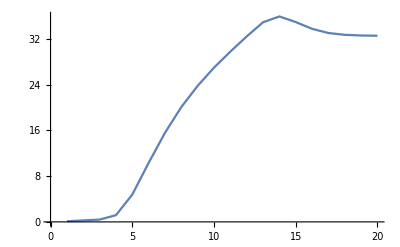

```mathematica
ListLinePlot[x1]
```

#### We will now repeat the result over a biased distribution.

```mathematica
f[x_]:=StringJoin[Map[ToString,x]]
```

```mathematica
dist = PadRight[ConstantArray[1,3],20]
```

{1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
x2 = Table[
Mean[
Table[
Block[
{
r1 =  f[RandomChoice[dist, 100]],
r2= f[RandomChoice[dist, 100]],
nPar = Length[StringPartition[f[RandomChoice[dist, 100]],i,i]]
},
StringBDMC2[r1, r2, i, i]/nPar (* we divide between the number of partitions.*)
]
,{j,15000} (* Number of samples *)
]//N
],{i,20}
]
```

{0.0944519,0.205447,0.404983,0.926152,2.09107,4.12816,6.79768,10.0354,13.4085,16.8845,20.3213,23.7061,26.7672,29.3934,31.5998,32.4942,32.9701,32.147,31.2576,31.1953}

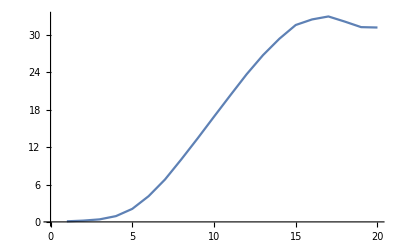

```mathematica
ListLinePlot[x2]
```

And now, both curves plotted together.

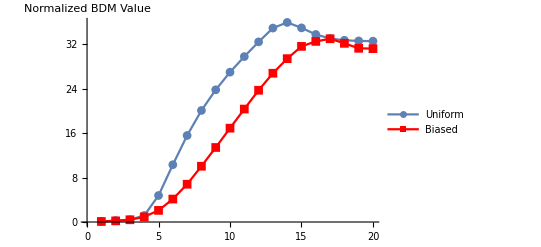

```mathematica
ListLinePlot[{x1,x2}, 
PlotStyle->{"97", Red},
PlotRangeClipping->False,
PlotMarkers->Automatic,
PlotLegends->
  Placed[LineLegend[{"Uniform","Biased"},
LegendFunction->(Framed[#,RoundingRadius->5]&),
LegendMargins->5],{0.80,0.23}],
AxesLabel->{None,"Normalized BDM Value"}]
```

```mathematica
dist2 = PadRight[ConstantArray[1,5],20]
```

{1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
x3 = Table[
Mean[
Table[
Block[
{
r1 =  f[RandomChoice[dist2, 100]],
r2= f[RandomChoice[dist2, 100]],
nPar = Length[StringPartition[f[RandomChoice[dist, 100]],i,i]]
},
StringBDMC2[r1, r2, i, i]/nPar (* we divide between the number of partitions.*)
]
,{j,15000} (* Number of samples *)
]//N
],{i,20}
]
```

{0.101342,0.228376,0.436238,1.16306,3.08628,6.4942,10.756,15.4161,19.7053,23.5474,26.8635,29.8001,32.352,34.1955,34.8514,34.2483,33.4069,32.4227,31.7513,31.5272}

```mathematica
dist3 = PadRight[ConstantArray[1,7],20]
```

{1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
x4 = Table[
Mean[
Table[
Block[
{
r1 =  f[RandomChoice[dist3, 100]],
r2= f[RandomChoice[dist3, 100]],
nPar = Length[StringPartition[f[RandomChoice[dist, 100]],i,i]]
},
StringBDMC2[r1, r2, i, i]/nPar (* we divide between the number of partitions.*)
]
,{j,15000} (* Number of samples *)
]//N
],{i,20}
]
```

{0.104741,0.249104,0.417382,1.21995,3.98901,8.77063,13.918,18.6825,22.6977,26.0905,29.0277,31.6885,34.1296,35.5116,35.0669,33.9738,33.0394,32.4936,32.1937,32.0647}

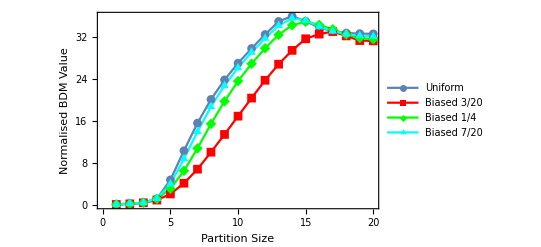

```mathematica
ListLinePlot[{x1,x2,x3, x4}, 
PlotStyle->{"97", Red, Green, Cyan},
PlotRangeClipping->False,
PlotMarkers->Automatic,
PlotLegends->
  Placed[LineLegend[{"Uniform","Biased 3/20", "Biased 1/4", "Biased 7/20"},
LegendFunction->(Framed[#,RoundingRadius->4]&),
LegendMargins->5],{0.20,0.73}],
Frame->True,
FrameLabel->{"Partition Size","Normalised BDM Value"}
]
```

We can see if the behavior changes by including overlapping.

```mathematica
y = Table[
Mean[
Table[
Block[
{
r1 =  StringJoin[Map[ToString,random[20]]],
r2= StringJoin[Map[ToString,random[20]]],
nPar = Length[Partition[r1,i,1]]
},
StringBDMC2[r1, r2, i, 1]/nPar
]
,{j,1000}(* Number of samples *)
] //N
],{i,20}
]
```

{0.289366,0.365781,0.528753,1.91368,5.6256,10.6686,15.7416,19.9913,23.7034,26.9827,29.7507,32.3802,34.9075,35.8705,34.9357,33.7279,33.039,32.7178,32.5622,32.4957}

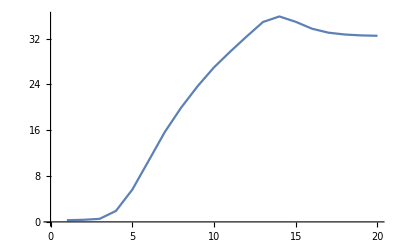

```mathematica
ListLinePlot[y]
```

As expected, the maximum value is where the transition from CTM to BDM, the drop is because we start using BDM instead of CTM for big partition sizes.

#### Conditional BDM Over Biased Strings.

Lets start with two random strings generated over a biased distribution.

```mathematica
r1b =RandomChoice[{0,0,1},20]
```

{0,0,0,1,1,0,1,0,0,0,0,0,0,0,0,0,0,1,1,0}

```mathematica
r2b = RandomChoice[{0,0,1},20]
```

{0,0,1,0,0,0,0,1,0,1,0,1,1,1,0,1,1,1,1,0}

```mathematica
Statistics`Library`NConditionalEntropy[r1b,r2b]
```

0.990331

As I have shown that makes little sense to consider block entropy, In this little experiment I will focus on conditional BDM with partition size of 1.

```mathematica
r1bS=StringJoin[Map[ToString,r1b]]
```

00011010000000000110

```mathematica
r2bS=StringJoin[Map[ToString,r2b]]
```

00100001010111011110

```mathematica
StringBDMC2[r1bS,r2bS,1,1]
```

6.22882

As shown bellow, this value is lower than the one’s from unrelated strings, as they give us less information from each other.

```mathematica
StringBDMC2[r1S,r2S,1,1]
```

0.

We can repeat this experiment over a big sample set to get an approximation to the expected quotient.

```mathematica
f[x_]:=StringJoin[Map[ToString,x]]
```

```mathematica
f[r1]
```

11000101110111010101

```mathematica
x = Table[
Mean[
Table[
Block[
{
dist = PadRight[ConstantArray[1,j],20]
},
Block[{
s=SeedRandom[RandomInteger[{0,999*10^9}]],
r1 = f[RandomChoice[dist, 20]],
r2= f[RandomChoice[dist, 20]],
(*Random unrelated String*)
rU =f[random[20]]
},(StringBDMC2[r1,r2,1,1]+1)/(StringBDMC2[r1,rU,1,1]+1)
]
]
,{i,15000}]
],{j,19}
]
```

{0.851309,0.872752,0.902887,0.966062,1.0694,1.21875,1.37138,1.49729,1.59724,1.58663,1.59312,1.50629,1.35413,1.19578,1.07009,0.964289,0.899351,0.87754,0.85811}

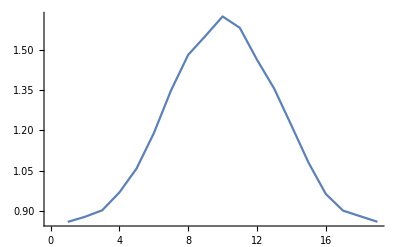

```mathematica
p1=ListLinePlot[x]
```

```mathematica
{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
PadRight[ConstantArray[1,20],20]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

Lets compare this behavior with Conditional Entropy.

```mathematica
y = Table[
Mean[
Table[
Block[
{
dist = PadRight[ConstantArray[1,j],20]
},
Block[{
r1 = RandomChoice[dist, 20],
r2= RandomChoice[dist, 20],
(*Random unrelated String*)
rU =random[20]
},(Statistics`Library`NConditionalEntropy[r1,r2]+1)/(Statistics`Library`NConditionalEntropy[r1,rU]+1)
]
]
,{i,15000}]
],{j,19}
]
```

{0.641184,0.73075,0.801518,0.858011,0.902927,0.938925,0.966559,0.986934,0.996707,1.00118,0.997431,0.986743,0.966975,0.940468,0.902674,0.857799,0.801615,0.73242,0.639953}

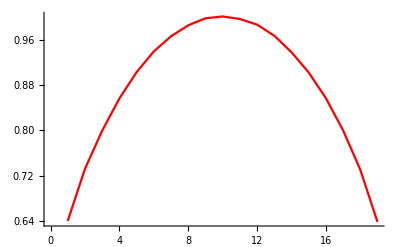

```mathematica
p2=ListLinePlot[y, PlotStyle->Red]
```

Lets normalize and combine both plots.

#### Trying to put legends on the plots.

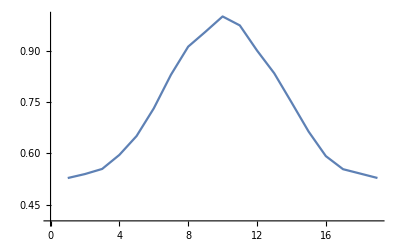

```mathematica
p1 = ListLinePlot[x/Max[x],PlotRange->{{0,19},{0.4,1}}, PlotLegends->"Conditional BDM"]
```

```mathematica
x
```

{0.851309,0.872752,0.902887,0.966062,1.0694,1.21875,1.37138,1.49729,1.59724,1.58663,1.59312,1.50629,1.35413,1.19578,1.07009,0.964289,0.899351,0.87754,0.85811}

```mathematica
y
```

{0.641184,0.73075,0.801518,0.858011,0.902927,0.938925,0.966559,0.986934,0.996707,1.00118,0.997431,0.986743,0.966975,0.940468,0.902674,0.857799,0.801615,0.73242,0.639953}

```mathematica
Range[19,19+19]
```

{19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38}

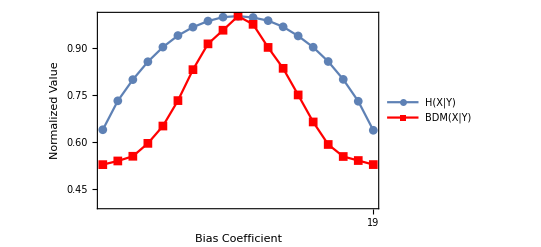

```mathematica
ListLinePlot[{y/Max[y],x/ Max[x]}, 
PlotRange->{{1,19},{0.4,1}},
PlotStyle->{"97", Red},
PlotRangeClipping->False,
PlotMarkers->Automatic,
FrameTicks->{Range[19,19+18], Automatic},
PlotLegends->
  Placed[LineLegend[{"H(X|Y)","BDM(X|Y)"},
LegendFunction->(Framed[#,RoundingRadius->1]&),
LegendMargins->5],{0.51,0.23}],
Frame->True,
FrameLabel->{"Bias Coefficient","Normalized Value"}
]
```